### Подгружаем данные

В первом датасете каждая строка представляет собой встречу (в пределах 50 м) между двумя пользователями. Первый столбец - шаг по времени в виде целого числа. В столбцах 2 и 3 указаны идентификационные номера пользователей. В столбце 4 указано расстояние между пользователями на данном временном шаге, округленное до ближайшего метра.

```mathematica
KisslerDataS1=Import["https://raw.githubusercontent.com/skissler/haslemere/master/Kissler_DataS1.csv"];
(*KisslerDataS1=Import[FileNameJoin[{NotebookDirectory[],"Kissler_DataS1.csv"}],"CSV"];*)
```

Соответствие шага по времени из первого столбца между индексами времени в реальное время по британскому стандартному времени (BST).

```mathematica
KisslerDataS2=Import["https://raw.githubusercontent.com/skissler/haslemere/master/Kissler_DataS2.csv"];
(*KisslerDataS2=Import[FileNameJoin[{NotebookDirectory[],"Kissler_DataS2.csv"}],"CSV"];*)
```

### Обрабатываем данные

#### Приводим KisslerDataS1 к виду {{{1,...,...,...},{1,...,...,...},...},{{2,...,...,...},{2,...,...,...},...},...,{{576,...,...,...},{576,...,...,...},...}} получая таким образом последовательность из списков где каждый список представляет собой состояние сети в определенный момент времени.

```mathematica
datasep=Table[Cases[KisslerDataS1,{i,_,_,_}],{i,1,Length[KisslerDataS2]}];
```

#### Копия сети где отброшены все ребра с расстоянием более 5 метров.

```mathematica
datasep5m=Table[Cases[datasep⟦i⟧,{_,_,_,x_Integer}/;x≤5],{i,1,Length[datasep]}];
```

#### Создаем для каждого временного состояния список ребер.

```mathematica
edgelist=Table[Table[datasep⟦j,i,2⟧<->datasep⟦j,i,3⟧,{i,1,Length[datasep⟦j⟧]}],{j,1,Length[datasep]}];
```

```mathematica
edgelist5m=Table[Table[datasep5m⟦j,i,2⟧<->datasep5m⟦j,i,3⟧,{i,1,Length[datasep5m⟦j⟧]}],{j,1,Length[datasep5m]}];
```

#### В исследуемой сети у всех ребер есть расстояния.

```mathematica
edgelength=Table[Table[N[datasep⟦j,i,4⟧],{i,1,Length[datasep⟦j⟧]}],{j,1,Length[datasep]}];
```

```mathematica
edgelength5m=Table[Table[N[datasep5m⟦j,i,4⟧],{i,1,Length[datasep5m⟦j⟧]}],{j,1,Length[datasep5m]}];
```

#### Предполагая, что вероятность заражения падает экспоненциально с расстоянием, введем коэффициент равный обратной экспоненте от расстояния.

```mathematica
w=ⅇ^-edgelength;
```

```mathematica
w5m=ⅇ^-edgelength5m;
```

#### Функция объединения сети в более широкие временные рамки.

Входные данные: список ребер, веса ребер, первая временная отсечка, последняя временная отсечка, количество временных шагов, которое мы объединяем в один шаг. Выходные данные: список ребер, веса ребер.

```mathematica
NetUnion[el_,we_,tstart_,tend_,tstep_]:=Module[{data=Table[Normal[GroupBy[{Flatten[el⟦i;;i+tstep-1⟧],Flatten[we⟦i;;i+tstep-1⟧]}ᵀ,First]]⟦All,2⟧,{i,1,tend-tstep+1,3}]},data=Table[{DeleteDuplicates[Flatten[data⟦i,All,All,1⟧]],Total[data⟦i,All,All,2⟧,{-1}]/tstep},{i,1,(tend-tstart+1)/tstep}];data]
```

```mathematica
delta={3,6,12,48,192,576};
```

```mathematica
nu=Table[NetUnion[edgelist,w,1,576,delta⟦j⟧],{j,1,Length[delta]}];
```

```mathematica
nu5m=Table[NetUnion[edgelist5m,w5m,1,576,delta⟦j⟧],{j,1,Length[delta]}];
```

```mathematica
timedata=Append[Append[Table[Table[KisslerDataS2⟦i,2⟧,{i,1,576,delta⟦j⟧}],{j,1,Length[delta]-2}],{"Thu 12 Oct 2017","Fri 13 Oct 2017", "Sat 14 Oct 2017"}],{"12-14 Oct 2017"}];
```

#### Подсчитаем количество уникальных вершин в сети за всё время наблюдений.

```mathematica
vertexcount=VertexCount[Graph[nu⟦-1,1,1⟧]];
```

```mathematica
vertexcount5m=VertexCount[Graph[nu5m⟦-1,1,1⟧]];
```

#### Создадим сетку с вершинами.

```mathematica
grid=Partition[Flatten[Table[{i,j},{i,1,Ceiling[√vertexcount]},{j,1,Ceiling[√vertexcount]}]],2]⟦1;;vertexcount⟧;
```

#### Координаты вершин полученные силовым методом укладки графа.

```mathematica
altgrid=Module[{g=Graph[nu⟦-1,1,1⟧,GraphLayout->"SpringElectricalEmbedding"]},SortBy[{VertexList[g],AnnotationValue[{g,#},VertexCoordinates]&/@VertexList[g]}ᵀ,First]];
```

```mathematica
altgrid5m=Module[{g=Graph[nu5m⟦-1,1,1⟧,GraphLayout->"SpringElectricalEmbedding"]},SortBy[{VertexList[g],AnnotationValue[{g,#},VertexCoordinates]&/@VertexList[g]}ᵀ,First]];
```

#### Визуализация сети.

```mathematica
vis=Table[Grid[{{timedata⟦k,j⟧},{EdgeAdd[AdjacencyGraph[Table[0,{i,1,vertexcount},{j,1,vertexcount}]],nu⟦k,j,1⟧,VertexCoordinates->Table[i->grid⟦i⟧,{i,1,vertexcount}],EdgeStyle->Table[nu⟦k,j,1,i⟧->Thickness[0.01nu⟦k,j,2,i⟧],{i,1,Length[nu⟦k,j,1⟧]}],ImageSize->Large]}}],{k,1,Length[nu]},{j,1,Length[nu⟦k⟧]}];
```

```mathematica
vis5m=Table[Grid[{{timedata⟦k,j⟧},{EdgeAdd[AdjacencyGraph[Table[0,{i,1,vertexcount},{j,1,vertexcount}]],nu5m⟦k,j,1⟧,VertexCoordinates->Table[i->grid⟦i⟧,{i,1,vertexcount}],EdgeStyle->Table[nu5m⟦k,j,1,i⟧->Thickness[0.01nu5m⟦k,j,2,i⟧],{i,1,Length[nu5m⟦k,j,1⟧]}],ImageSize->Large]}}],{k,1,Length[nu5m]},{j,1,Length[nu5m⟦k⟧]}];
```

### Визуализация сети в виде квадратной решетки

#### За всё время

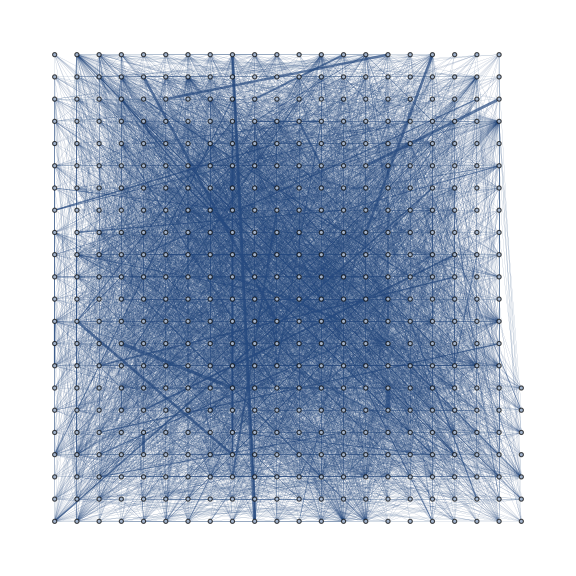
12-14 Oct 2017
-Graphics-

```mathematica
vis⟦-1,1⟧
```

#### За всё время (отсечка в 5м)

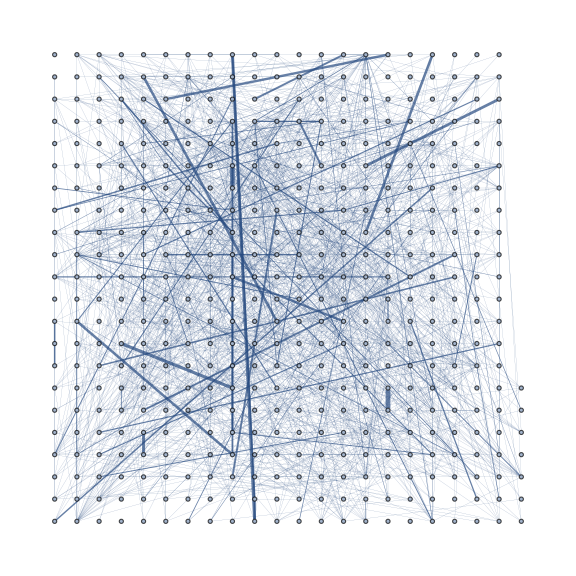
12-14 Oct 2017
-Graphics-

```mathematica
vis5m⟦-1,1⟧
```

```mathematica
NearestNeighborList[graph_]:=Module[{el=EdgeList[graph],vl=VertexList[graph],data={}},data=Sort[{Flatten[{el⟦All,1⟧,el⟦All,2⟧}],Flatten[{el⟦All,2⟧,el⟦All,1⟧}]}ᵀ];data=Table[Cases[data,{vl⟦i⟧,_}]⟦All,2⟧,{i,1,Length[vl]}];data]
```

```mathematica
SIR[graph_,i0_,β_,μ_,t_]:=Module[{vc=VertexCount[graph],data={VertexList[graph],NearestNeighborList[graph],ConstantArray["Susceptible",VertexCount[graph]]}ᵀ,out=ConstantArray[{},t+1],iv={},pos=0},out⟦1⟧={vc-i0,i0,0};iv=RandomSample[Range[vc],i0];Do[data⟦iv⟦i⟧,3⟧="Infected",{i,1,i0}];Do[iv=Cases[data,{_,_,"Infected"}];Do[Do[If[RandomChoice[{β,1-β}->{True,False}]==True,pos=FirstPosition[data,{iv⟦j,2,k⟧,_,_},Missing["NotFound"],1]⟦1⟧;If[data⟦pos,3⟧=="Susceptible",data⟦pos,3⟧="Infected"]],{k,1,Length[iv⟦j,2⟧]}],{j,1,Length[iv]}];Do[If[RandomChoice[{μ,1-μ}->{True,False}]==True,data⟦FirstPosition[data⟦All,1⟧,iv⟦j,1⟧]⟦1⟧,3⟧="Recovered"],{j,1,Length[iv]}];out⟦i⟧={Length[Cases[data,{_,_,"Susceptible"}]],Length[Cases[data,{_,_,"Infected"}]],Length[Cases[data,{_,_,"Recovered"}]]},{i,2,t+1}];out={{Range[0,t],out⟦All,1⟧}ᵀ,{Range[0,t],out⟦All,2⟧}ᵀ,{Range[0,t],out⟦All,3⟧}ᵀ};out]
```

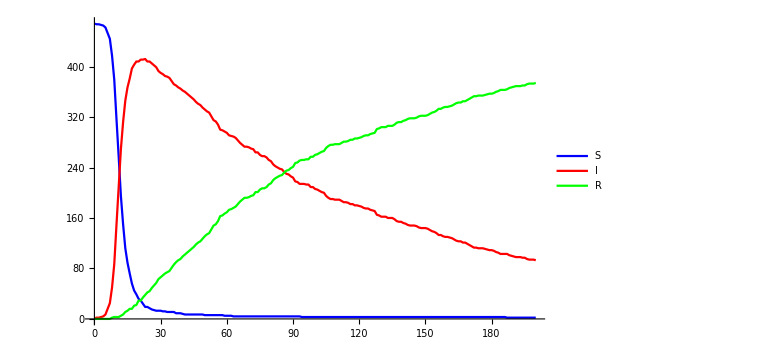

```mathematica
ListLinePlot[SIR[nu⟦-1,1,1⟧,1,0.02,0.01,200],PlotStyle->{Blue,Red,Green},PlotLegends->{"S","I","R"},ImageSize->Large]
```

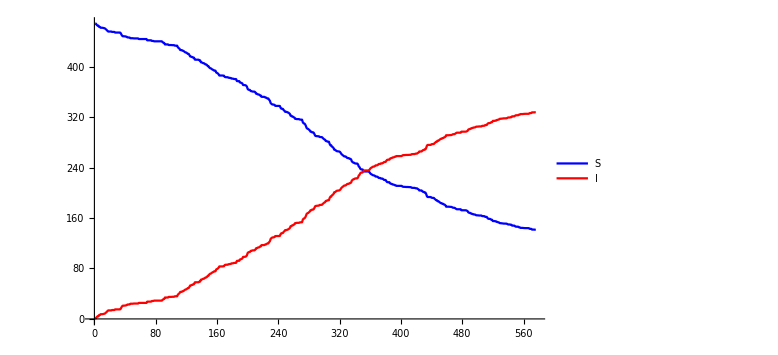

```mathematica
ListLinePlot[{data⟦330,1⟧,data⟦330,2⟧},PlotStyle->{Blue,Red},PlotLegends->{"S","I"},ImageSize->Large]
```

```mathematica
Export[FileNameJoin[{NotebookDirectory[],"s6.png"}],Out[59]]
```

C:\Users\muha4\OneDrive\Диплом\s6.png

```mathematica
nu⟦1,1,1⟧
```

{1<->390,2<->215,2<->246,2<->265,5<->367,5<->430,8<->10,9<->274,11<->22,11<->39,12<->342,13<->437,14<->202,14<->307,14<->357,15<->238,15<->371,17<->372,17<->395,19<->30,19<->60,19<->403,19<->411,26<->102,26<->426,27<->134,29<->79,29<->187,30<->60,30<->287,30<->403,30<->411,31<->45,32<->180,32<->195,35<->253,35<->400,36<->301,36<->457,38<->452,39<->78,39<->367,40<->73,40<->424,46<->83,46<->163,46<->380,48<->160,48<->295,48<->318,48<->332,49<->234,49<->389,49<->449,52<->56,52<->120,54<->319,60<->287,60<->403,60<->411,61<->320,64<->149,64<->250,65<->84,65<->227,67<->443,68<->186,69<->456,74<->262,75<->126,75<->183,76<->229,76<->311,76<->448,77<->144,80<->245,80<->363,82<->411,82<->440,83<->163,83<->380,84<->227,84<->370,84<->421,84<->468,85<->111,86<->127,86<->190,86<->388,87<->164,87<->174,88<->111,88<->142,88<->159,88<->443,90<->243,90<->323,90<->446,92<->93,94<->158,94<->409,95<->106,95<->107,99<->176,99<->224,99<->386,101<->438,102<->426,104<->324,105<->287,106<->107,106<->211,107<->211,108<->364,109<->162,109<->230,109<->416,110<->352,111<->142,111<->159,114<->138,118<->129,118<->302,121<->387,121<->455,122<->141,123<->255,126<->183,127<->190,127<->388,129<->302,130<->218,131<->312,133<->205,133<->339,133<->465,136<->202,136<->355,136<->422,137<->442,142<->159,142<->445,146<->271,147<->233,149<->250,153<->340,153<->341,155<->354,155<->369,158<->409,159<->445,160<->168,160<->318,160<->332,162<->230,162<->416,163<->380,164<->174,164<->272,165<->216,166<->170,166<->327,166<->423,168<->343,169<->273,169<->286,170<->327,176<->224,176<->386,179<->235,180<->195,181<->189,181<->276,181<->378,187<->242,188<->296,189<->276,189<->378,190<->388,192<->193,198<->199,198<->200,199<->200,202<->307,202<->357,202<->422,204<->322,204<->396,205<->339,205<->465,210<->434,215<->246,215<->265,217<->228,217<->283,218<->274,223<->345,223<->415,224<->386,227<->370,227<->421,227<->468,228<->283,229<->237,230<->416,234<->389,238<->371,243<->323,243<->335,243<->446,244<->453,245<->363,246<->265,253<->400,261<->281,268<->428,268<->447,273<->286,276<->378,279<->290,282<->284,286<->311,295<->318,295<->332,298<->319,301<->457,307<->357,308<->467,309<->310,311<->448,318<->332,322<->396,323<->335,323<->446,325<->460,327<->423,334<->418,336<->337,339<->465,340<->341,345<->415,348<->393,354<->369,355<->422,361<->375,362<->420,367<->430,370<->421,370<->468,372<->395,375<->429,381<->382,387<->455,389<->449,403<->411,404<->431,411<->440,414<->444,421<->468,428<->447,439<->445,2<->21,3<->4,19<->26,19<->320,26<->30,26<->60,26<->287,26<->320,26<->403,26<->411,30<->320,42<->58,44<->395,54<->153,60<->320,64<->169,102<->442,122<->227,141<->227,149<->169,160<->295,201<->444,215<->361,215<->429,233<->273,233<->286,273<->311,276<->330,276<->375,320<->403,330<->375,426<->442,3<->234,3<->389,130<->352,215<->375,218<->352,271<->459}

```mathematica
NNL[el_,ew_,vc_]:=Module[{data=Sort[Partition[Flatten[{{el⟦All,1⟧,el⟦All,2⟧,ew}ᵀ,{el⟦All,2⟧,el⟦All,1⟧,ew}ᵀ}],3]]},data=Table[{Cases[data,{i,_,_}]⟦All,2⟧,Cases[data,{i,_,_}]⟦All,3⟧},{i,1,vc}];data]
```

```mathematica
SIR2[ele_,ewe_,vc_,i0_,β_,μ_]:=Module[{predata=Table[NNL[ele⟦i⟧,ewe⟦i⟧,vc],{i,1,Length[ele]}],data=Table[{i,"Susceptible",{},{}},{j,1,Length[ele]},{i,1,vc}],sv={},iv={},rv={},pos={}},Do[Do[data⟦i,j,3⟧=predata⟦i,j,1⟧;data⟦i,j,4⟧=predata⟦i,j,2⟧,{j,1,vc}],{i,1,Length[ele]}];iv=RandomSample[Range[vc],i0];Do[data⟦1,iv⟦i⟧,2⟧="Infected",{i,1,i0}];Do[rv=Cases[data⟦i⟧,{_,"Recovered",_,_}];If[rv≠{},Do[data⟦i+1,rv⟦j,1⟧,2⟧="Recovered",{j,1,Length[rv]}]];iv=Cases[data⟦i⟧,{_,"Infected",_,_}];If[iv≠{},Do[data⟦i+1,iv⟦j,1⟧,2⟧="Infected",{j,1,Length[iv]}];Do[If[iv⟦j,3⟧≠{},Do[If[RandomChoice[{iv⟦j,4,k⟧,1-iv⟦j,4,k⟧}->{True,False}]==True,If[data⟦i,iv⟦j,3,k⟧,2⟧=="Susceptible",data⟦i+1,iv⟦j,3,k⟧,2⟧="Infected"]],{k,1,Length[iv⟦j,3⟧]}]],{j,1,Length[iv]}];Do[If[RandomChoice[{μ,1-μ}->{True,False}]==True,data⟦i+1,iv⟦j,1⟧,2⟧="Recovered"],{j,1,Length[iv]}]],{i,1,Length[ele]-1}];data]
```

```mathematica
SIR2a[ele_,ewe_,vc_,i0_,β_,μ_]:=Module[{predata=Table[NNL[ele⟦i⟧,ewe⟦i⟧,vc],{i,1,Length[ele]}],data=Table[{i,"Susceptible",{},{}},{j,1,Length[ele]},{i,1,vc}],sv={},iv={},rv={},pos={}},Do[Do[data⟦i,j,3⟧=predata⟦i,j,1⟧;data⟦i,j,4⟧=predata⟦i,j,2⟧,{j,1,vc}],{i,1,Length[ele]}];data⟦1,i0,2⟧="Infected";Do[rv=Cases[data⟦i⟧,{_,"Recovered",_,_}];If[rv≠{},Do[data⟦i+1,rv⟦j,1⟧,2⟧="Recovered",{j,1,Length[rv]}]];iv=Cases[data⟦i⟧,{_,"Infected",_,_}];If[iv≠{},Do[data⟦i+1,iv⟦j,1⟧,2⟧="Infected",{j,1,Length[iv]}];Do[If[iv⟦j,3⟧≠{},Do[If[RandomChoice[{iv⟦j,4,k⟧,1-iv⟦j,4,k⟧}->{True,False}]==True,If[data⟦i,iv⟦j,3,k⟧,2⟧=="Susceptible",data⟦i+1,iv⟦j,3,k⟧,2⟧="Infected"]],{k,1,Length[iv⟦j,3⟧]}]],{j,1,Length[iv]}];Do[If[RandomChoice[{μ,1-μ}->{True,False}]==True,data⟦i+1,iv⟦j,1⟧,2⟧="Recovered"],{j,1,Length[iv]}]],{i,1,Length[ele]-1}];data]
```

```mathematica
td01=SIR2a[edgelist,w,vertexcount,1,1,0];
```

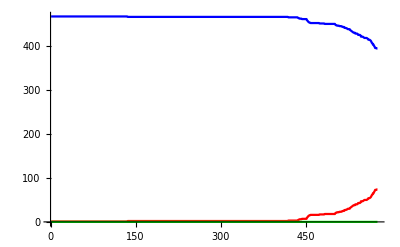

```mathematica
ListLinePlot[{Table[{i,Length[Cases[td01⟦i⟧,{_,"Susceptible",_,_}]]},{i,1,Length[td01]}],Table[{i,Length[Cases[td01⟦i⟧,{_,"Infected",_,_}]]},{i,1,Length[td01]}],Table[{i,Length[Cases[td01⟦i⟧,{_,"Recovered",_,_}]]},{i,1,Length[td01]}]},PlotStyle->{Blue,Red,Green}]
```

```mathematica
tv=ReverseSortBy[{Table[i,{i,1,vertexcount}],N[Mean[Table[Module[{g=EdgeAdd[AdjacencyGraph[Table[0,{i,1,vertexcount},{j,1,vertexcount}]],edgelist⟦k⟧]},SortBy[{VertexList[g],VertexDegree[g]}ᵀ,First]⟦All,2⟧],{k,1,Length[edgelist]}]]]}ᵀ,Last]⟦1,1⟧
```

216

```mathematica
td02=SIR2a[edgelist,w,vertexcount,tv,1,0];
```

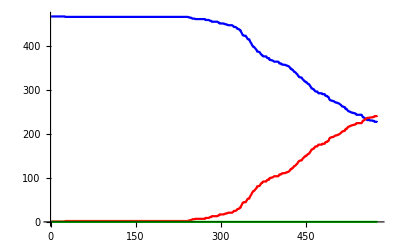

```mathematica
ListLinePlot[{Table[{i,Length[Cases[td02⟦i⟧,{_,"Susceptible",_,_}]]},{i,1,Length[td02]}],Table[{i,Length[Cases[td02⟦i⟧,{_,"Infected",_,_}]]},{i,1,Length[td02]}],Table[{i,Length[Cases[td02⟦i⟧,{_,"Recovered",_,_}]]},{i,1,Length[td02]}]},PlotStyle->{Blue,Red,Green}]
```

```mathematica
tv100=ReverseSortBy[{Table[i,{i,1,vertexcount}],N[Mean[Table[Module[{g=EdgeAdd[AdjacencyGraph[Table[0,{i,1,vertexcount},{j,1,vertexcount}]],edgelist5m⟦k⟧]},SortBy[{VertexList[g],VertexDegree[g]}ᵀ,First]⟦All,2⟧],{k,1,100}]]]}ᵀ,Last]⟦1,1⟧
```

15

```mathematica
td03=SIR2a[edgelist,w,vertexcount,tv100,1,0];
```

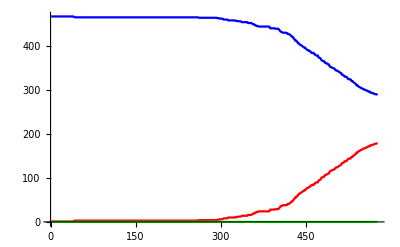

```mathematica
ListLinePlot[{Table[{i,Length[Cases[td03⟦i⟧,{_,"Susceptible",_,_}]]},{i,1,Length[td03]}],Table[{i,Length[Cases[td03⟦i⟧,{_,"Infected",_,_}]]},{i,1,Length[td03]}],Table[{i,Length[Cases[td03⟦i⟧,{_,"Recovered",_,_}]]},{i,1,Length[td03]}]},PlotStyle->{Blue,Red,Green}]
```

```mathematica
SIR2b[ele_,ewe_,vc_,i0_,β_,μ_]:=Module[{predata=Table[NNL[ele⟦i⟧,ewe⟦i⟧,vc],{i,1,Length[ele]}],data=Table[{i,"Susceptible",{},{}},{j,1,Length[ele]},{i,1,vc}],sv={},iv={},rv={},pos={}},Do[Do[data⟦i,j,3⟧=predata⟦i,j,1⟧;data⟦i,j,4⟧=predata⟦i,j,2⟧,{j,1,vc}],{i,1,Length[ele]}];data⟦1,i0,2⟧="Infected";Do[rv=Cases[data⟦i⟧,{_,"Recovered",_,_}];If[rv≠{},Do[data⟦i+1,rv⟦j,1⟧,2⟧="Recovered",{j,1,Length[rv]}]];iv=Cases[data⟦i⟧,{_,"Infected",_,_}];If[iv≠{},Do[data⟦i+1,iv⟦j,1⟧,2⟧="Infected",{j,1,Length[iv]}];Do[If[iv⟦j,3⟧≠{},Do[If[RandomChoice[{iv⟦j,4,k⟧,1-iv⟦j,4,k⟧}->{True,False}]==True,If[data⟦i,iv⟦j,3,k⟧,2⟧=="Susceptible",data⟦i+1,iv⟦j,3,k⟧,2⟧="Infected"]],{k,1,Length[iv⟦j,3⟧]}]],{j,1,Length[iv]}];Do[If[RandomChoice[{μ,1-μ}->{True,False}]==True,data⟦i+1,iv⟦j,1⟧,2⟧="Recovered"],{j,1,Length[iv]}]],{i,1,Length[ele]-1}];{Table[Length[Cases[data⟦i⟧,{_,"Susceptible",_,_}]],{i,1,Length[data]}],Table[Length[Cases[data⟦i⟧,{_,"Infected",_,_}]],{i,1,Length[data]}],Table[Length[Cases[data⟦i⟧,{_,"Recovered",_,_}]],{i,1,Length[data]}]}]
```

```mathematica
td04=N[Mean[Table[SIR2b[edgelist,w,vertexcount,1,1,0],{l,1,100}]]];
```